```mathematica
ClearAll["Global`*"];
(* The below definition of bInv maps the [0,1] interval into [0,∞] *)
(* It also derives the inverse of the function, which (for real b) is below *)
Solve[{b==Log[1/(1-bInv)]},bInv][[1]]
```

{bInv→ConditionalExpression[ⅇ^-b (-1+ⅇ^b),-π<Im[b]≤π]}

```mathematica
ClearAll["Global`*"];
Þ=(R β)^(1/ρ)
Subscript[Þ, R]=Þ/R
Subscript[Þ, Γ]=Þ/Γ
κ=1-Subscript[Þ, R]
h=0/(1-Γ/R) (* Simplest case is where human wealth is zero *)
c = (b + h)κ (* = b κ when h=0 *)
b=Log[1/(1-bInv)] (* as above *)
cInv=(Exp[-c/κ](Exp[c/κ]-1)) (* Divide by κ so they are the same scale *)
```

(R β)^(1/ρ)

(R β)^(1/ρ)/R

(R β)^(1/ρ)/Γ

1-(R β)^(1/ρ)/R

0

b (1-(R β)^(1/ρ)/R)

((b (1-(R β)^(1/ρ)/R))^(1-ρ))/(1-ρ)

Log[1/(1-bInv)]

(-1+1/(1-bInv)) (1-bInv)

```mathematica
(* Pick some parameter values *)
```

```mathematica
{R,Γ}={1.05,1.02};
ρ=2;
β=0.94;
κ
```

0.0538298

```mathematica
(* Show the mapping of the [0-1] interval to [0,∞] *)
```

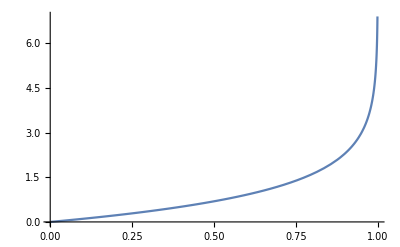

```mathematica
Plot[Log[1/(1-bInv)],{bInv,0.001,0.9999},PlotRange->All]
```

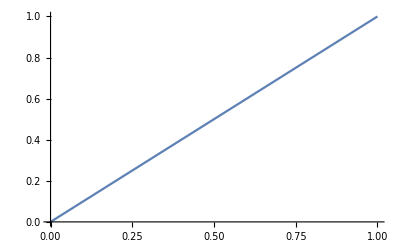

```mathematica
{bInvMin,bInvMax}={0.000001,0.999999}; (* Pick endpoints *)
bInv=bInvMin; bMin=b;cMin=c;
bInv=bInvMax; bMax=b; cMax=c;
bInvVScInv=Plot[cInv,{bInv,bInvMin,bInvMax}] (* cInv as a function of bInv *)
```

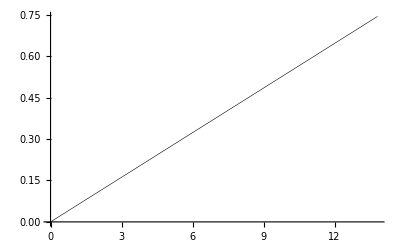

```mathematica
PlotInv=ParametricPlot[{b,c},{bInv,bInvMin,bInvMax},PlotRange->{{bMin,bMax},{cMin,cMax}},AspectRatio->1/GoldenRatio,PlotStyle->{Thickness[0.001],Black}]
```

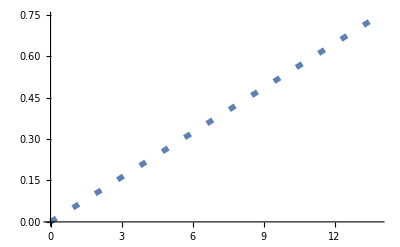

```mathematica
(* Plot the raw consumption function c= b κ *)
PlotRaw=Plot[κ bRaw,{bRaw,bMin,bMax},PlotRange->{{bMin,bMax},{cMin,cMax}},AspectRatio->1/GoldenRatio,PlotStyle->{Thickness[0.01],Dashing[{Small,Large}]}]
```

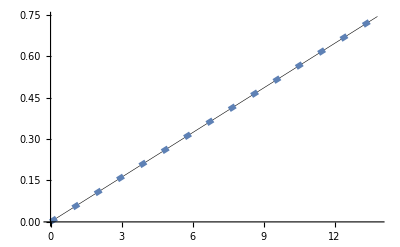

```mathematica
(* The inverted function is identical to the raw one *)
Show[PlotInv,PlotRaw]
```